## Heat equation on a grid graph

8

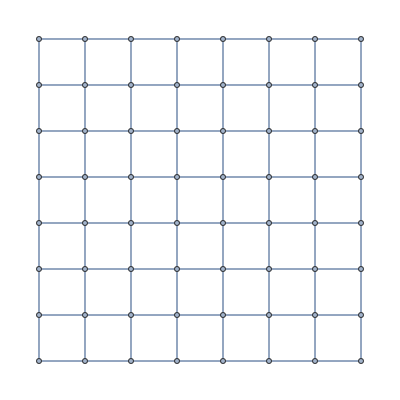

```mathematica
n=8
g=GridGraph[{n,n}]
```

```mathematica
EdgeList@g;
```

```mathematica
temperatureTable=Table[RandomReal[],n^2]
```

{0.87753,0.980112,0.407661,0.586659,0.574314,0.0338042,0.625966,0.119403,0.514926,0.670968,0.818908,0.661374,0.764215,0.626482,0.0588313,0.00414799,0.507698,0.494437,0.823896,0.847674,0.68872,0.446425,0.661919,0.379575,0.758002,0.769705,0.494975,0.803078,0.294829,0.902033,0.0707223,0.163531,0.0750002,0.765688,0.318714,0.826913,0.747634,0.564796,0.456145,0.473048,0.958902,0.731329,0.0139416,0.830945,0.140523,0.93231,0.128858,0.758132,0.850108,0.113806,0.324807,0.192989,0.542288,0.362989,0.102868,0.321693,0.294345,0.262994,0.847307,0.946136,0.330159,0.845902,0.615912,0.678427}

Color formatting reflects the value of the “temperature” scalar field at each vertex (The colors range between 0- dark blue and 1-red).

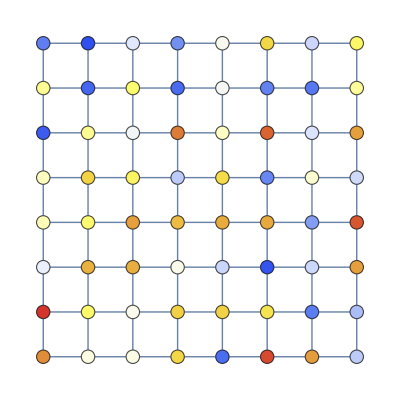

```mathematica
Graph[UndirectedEdge@@@g, VertexStyle->Thread[Range[n^2]->ColorData["TemperatureMap"]/@temperatureTable],VertexSize->0.3]
```

We model the heat distribution with the matrix Laplacian defined as the difference between the degree matrix and the adjacency matrix. Adjacency matrix is a {8^2,8^2} table encoding connections between the vertices (1-connected, 0-disconnected). Degree matrix is diagonal and the entries correspond to the number of edges connected to each vertex. There are several nice features of the grid undirected graph which would be absent otherwise:

Martix Laplacian is symmetric for undirected graphs

0 is an eigenvalue of the matrix Laplacian corresponding to eigenvector [1,...,1]. This leads to asymptotic equilibrium behaviour as t->∞, with the limit temperature being mean of the initial scalar field values.

```mathematica
adjMatrix[g_]:=Normal@AdjacencyMatrix[g];
Normal@AdjacencyMatrix[g]//MatrixForm;
```

```mathematica
degMatrix[g_]:=Normal@DiagonalMatrix[VertexDegree@g];
```

```mathematica
matrixLaplacian[g_]:=Normal@AdjacencyMatrix[g]-Normal@DiagonalMatrix[VertexDegree@g];
```

We make an arbitrary choice of the thermal conductivity and the timestep width

```mathematica
matrixLaplacian@g;
```

```mathematica
k=0.1;δt=0.1;
```

```mathematica
discreteLaplacian[g_,ϕ_]:=Dot[Normal@AdjacencyMatrix[g]-Normal@DiagonalMatrix[VertexDegree@g],ϕ]
```

We use the Euler Method for solving the discretized heat equation

```mathematica
eulerMethod[{g_,t_,ϕ_}]:={g,t+δt,ϕ+k*δt *discreteLaplacian[g,ϕ]}
```

The temperature after 100 steps (random initial condition):

```mathematica
NestList[eulerMethod,{g,0,temperatureTable},1000][[1000,3]]
```

{0.563316,0.558721,0.550175,0.538898,0.52655,0.515012,0.506096,0.501239,0.561543,0.557113,0.548872,0.537996,0.526085,0.514952,0.506349,0.501662,0.558261,0.554135,0.546457,0.53632,0.525215,0.514832,0.506806,0.502433,0.553962,0.550231,0.543287,0.534115,0.524061,0.514655,0.507381,0.503416,0.549292,0.545989,0.539837,0.531707,0.522788,0.514438,0.507976,0.504453,0.544964,0.542055,0.536633,0.529463,0.52159,0.514213,0.5085,0.505384,0.541643,0.539034,0.53417,0.527733,0.52066,0.514026,0.508885,0.50608,0.539842,0.537396,0.532834,0.526793,0.520151,0.513919,0.509088,0.506451}

As expected, the temperature distribution approaches a homogeneous state

## Wolfram model Approach

Circular initial condition

```mathematica
initialCircleCondition={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,2,0,0,0,0,0,2,2,2,2,0,0,0,0,2,2,2,2,0,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
```

Giffin’

```mathematica
N@Eigenvalues[Normal@AdjacencyMatrix[g]-Normal@DiagonalMatrix[VertexDegree@g]]
```

{-7.69552,-7.26197,-7.26197,-6.82843,-6.61313,-6.61313,-6.17958,-6.17958,-5.84776,-5.84776,-5.53073,-5.41421,-5.41421,-5.08239,-5.08239,-4.76537,-4.76537,-4.64885,-4.64885,-4.43355,-4.43355,-4.,-4.,-4.,-4.,-4.,-4.,-4.,-3.84776,-3.84776,-3.56645,-3.56645,-3.41421,-3.41421,-3.35115,-3.35115,-3.23463,-3.23463,-2.91761,-2.91761,-2.76537,-2.76537,-2.58579,-2.58579,-2.46927,-2.15224,-2.15224,-2.,-2.,-1.82042,-1.82042,-1.38687,-1.38687,-1.23463,-1.23463,-1.17157,-0.738027,-0.738027,-0.585786,-0.585786,-0.304482,-0.152241,-0.152241,0.}

```mathematica
graphToHypergraph[G_]:=Module[{subsets=Subsets[#,{1}]&/@AdjacencyList@G },Flatten[Table[Append[ #,(VertexList@G)[[i]]]&/@subsets[[i]],{i,VertexCount@g}],1]]
```

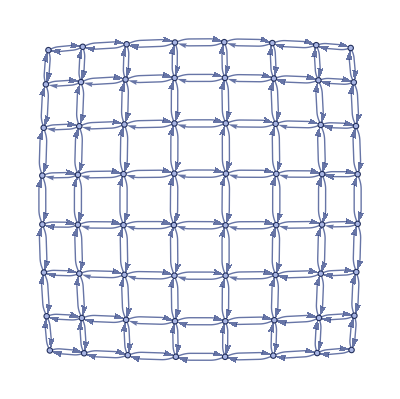

```mathematica
simpleGrid=ResourceFunction["WolframModelPlot"][graphToHypergraph@g]
```

```mathematica
graphToHypergraphNew[g_]:=Flatten[DeleteCases[Table[If[(Normal@AdjacencyMatrix@g)[[#]][[i]]*i==0,0,{#,i}],{i,VertexList@g}],0]&/@(VertexList@g),1]
```

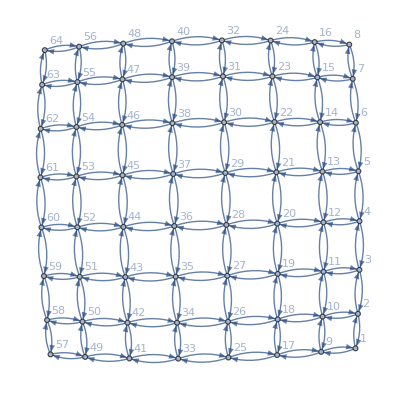

```mathematica
Graph[DirectedEdge@@#&/@graphToHypergraphNew@g,VertexLabels->Automatic]
```

```mathematica
hginhomogeneities={{1,2},{1,9},{2,1},{2,3},{2,10},{3,2},{3,4},{3,11},{4,3},{4,5},{4,12},{5,4},{5,6},{5,13},{6,7},{6,14},{7,6},{7,8},{7,15},{8,7},{8,16},{9,1},{9,10},{9,17},{10,2},{10,9},{10,11},{10,18},{11,3},{11,10},{11,12},{12,11},{12,13},{12,20},{13,5},{13,12},{13,14},{13,21},{14,6},{14,13},{14,15},{14,22},{15,7},{15,14},{15,16},{15,23},{16,8},{16,15},{16,24},{17,9},{17,18},{17,25},{18,10},{18,17},{18,19},{18,26},{19,11},{19,18},{19,20},{19,27},{20,12},{20,19},{20,21},{20,28},{21,13},{21,20},{21,22},{21,29},{22,14},{22,21},{22,23},{22,30},{23,15},{23,22},{23,24},{23,31},{24,16},{24,23},{24,32},{25,17},{25,26},{25,33},{26,18},{26,25},{26,27},{26,34},{27,19},{27,26},{27,28},{27,35},{28,20},{28,29},{28,36},{29,21},{29,30},{29,37},{30,22},{30,29},{30,31},{30,38},{31,23},{31,30},{31,32},{31,39},{32,24},{32,31},{32,40},{33,41},{34,26},{34,33},{34,35},{34,42},{35,27},{35,34},{35,36},{35,43},{36,28},{36,35},{36,37},{36,44},{37,29},{37,36},{37,38},{37,45},{38,30},{38,37},{38,39},{38,46},{39,31},{39,38},{39,40},{39,47},{40,32},{40,39},{40,48},{41,33},{41,42},{41,49},{42,34},{42,41},{42,43},{42,50},{43,35},{43,42},{43,44},{43,51},{44,36},{44,43},{44,45},{44,52},{45,37},{45,44},{45,46},{45,53},{46,38},{46,45},{46,47},{46,54},{47,39},{47,46},{47,48},{47,55},{48,40},{48,47},{48,56},{49,41},{49,50},{49,57},{50,42},{50,49},{50,51},{50,58},{51,50},{51,52},{51,59},{52,44},{52,51},{52,53},{52,60},{53,45},{53,52},{53,54},{53,61},{54,46},{54,53},{54,55},{54,62},{55,47},{55,56},{55,63},{56,48},{56,55},{56,64},{57,49},{57,58},{58,50},{58,57},{58,59},{59,60},{60,52},{60,59},{60,61},{61,53},{61,60},{61,62},{62,54},{62,61},{62,63},{63,55},{63,62},{63,64},{64,56},{64,63}}
```

{{1,2},{1,9},{2,1},{2,3},{2,10},{3,2},{3,4},{3,11},{4,3},{4,5},{4,12},{5,4},{5,6},{5,13},{6,7},{6,14},{7,6},{7,8},{7,15},{8,7},{8,16},{9,1},{9,10},{9,17},{10,2},{10,9},{10,11},{10,18},{11,3},{11,10},{11,12},{12,11},{12,13},{12,20},{13,5},{13,12},{13,14},{13,21},{14,6},{14,13},{14,15},{14,22},{15,7},{15,14},{15,16},{15,23},{16,8},{16,15},{16,24},{17,9},{17,18},{17,25},{18,10},{18,17},{18,19},{18,26},{19,11},{19,18},{19,20},{19,27},{20,12},{20,19},{20,21},{20,28},{21,13},{21,20},{21,22},{21,29},{22,14},{22,21},{22,23},{22,30},{23,15},{23,22},{23,24},{23,31},{24,16},{24,23},{24,32},{25,17},{25,26},{25,33},{26,18},{26,25},{26,27},{26,34},{27,19},{27,26},{27,28},{27,35},{28,20},{28,29},{28,36},{29,21},{29,30},{29,37},{30,22},{30,29},{30,31},{30,38},{31,23},{31,30},{31,32},{31,39},{32,24},{32,31},{32,40},{33,41},{34,26},{34,33},{34,35},{34,42},{35,27},{35,34},{35,36},{35,43},{36,28},{36,35},{36,37},{36,44},{37,29},{37,36},{37,38},{37,45},{38,30},{38,37},{38,39},{38,46},{39,31},{39,38},{39,40},{39,47},{40,32},{40,39},{40,48},{41,33},{41,42},{41,49},{42,34},{42,41},{42,43},{42,50},{43,35},{43,42},{43,44},{43,51},{44,36},{44,43},{44,45},{44,52},{45,37},{45,44},{45,46},{45,53},{46,38},{46,45},{46,47},{46,54},{47,39},{47,46},{47,48},{47,55},{48,40},{48,47},{48,56},{49,41},{49,50},{49,57},{50,42},{50,49},{50,51},{50,58},{51,50},{51,52},{51,59},{52,44},{52,51},{52,53},{52,60},{53,45},{53,52},{53,54},{53,61},{54,46},{54,53},{54,55},{54,62},{55,47},{55,56},{55,63},{56,48},{56,55},{56,64},{57,49},{57,58},{58,50},{58,57},{58,59},{59,60},{60,52},{60,59},{60,61},{61,53},{61,60},{61,62},{62,54},{62,61},{62,63},{63,55},{63,62},{63,64},{64,56},{64,63}}

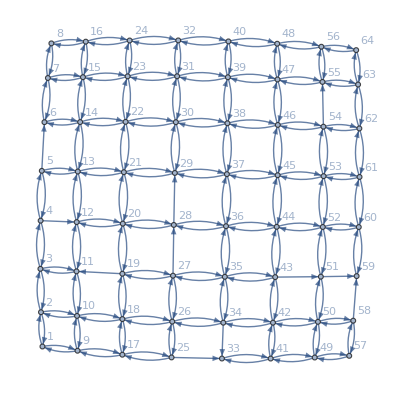

```mathematica
Graph[DirectedEdge@@#&/@hginhomogeneities,VertexLabels->Automatic]
```

```mathematica
g1=ResourceFunction["HypergraphToGraph"][hginhomogeneities,VertexLabels->Automatic]
```

-Graphics-

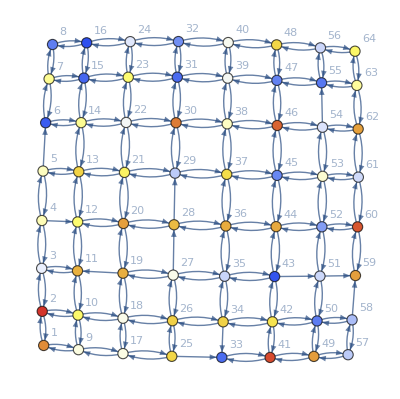

```mathematica
Graph[g1, VertexStyle->Thread[Range[n^2]->ColorData["TemperatureMap"]/@temperatureTable],VertexSize->0.3]
```

```mathematica
matrixLaplacian1[g_]:=Normal@AdjacencyMatrix[g]-1/2 Normal@DiagonalMatrix[VertexDegree@g];
k=0.1;δt=0.1;
discreteLaplacian1[g_,ϕ_]:=Dot[Normal@AdjacencyMatrix[g]-1/2 Normal@DiagonalMatrix[VertexDegree@g],ϕ]
eulerMethod1[{g_,t_,ϕ_}]:={g,t+δt,ϕ+k*δt *discreteLaplacian1[g,ϕ]}
```

```mathematica
N@Eigenvalues@matrixLaplacian[g1]
```

{-11.3855,-10.9807,-10.7336,-10.3679,-10.2177,-10.03,-9.84578,-9.61894,-9.42341,-9.34461,-8.98114,-8.82999,-8.77875,-8.56457,-8.47079,-8.19292,-8.08247+0.0262342 ⅈ,-8.08247-0.0262342 ⅈ,-7.93801,-7.79834,-7.6992,-7.53492,-7.33438+0.0398864 ⅈ,-7.33438-0.0398864 ⅈ,-7.31717,-7.0913,-7.01212+0.0432522 ⅈ,-7.01212-0.0432522 ⅈ,-6.94201,-6.87059,-6.85111,-6.6233,-6.49626+0.0679014 ⅈ,-6.49626-0.0679014 ⅈ,-6.44914,-6.34429,-6.14276+0.0268285 ⅈ,-6.14276-0.0268285 ⅈ,-5.85908+0.135341 ⅈ,-5.85908-0.135341 ⅈ,-5.7305+0.128141 ⅈ,-5.7305-0.128141 ⅈ,-5.54407,-5.48336,-5.28063,-5.2222+0.119012 ⅈ,-5.2222-0.119012 ⅈ,-5.05749+0.03511 ⅈ,-5.05749-0.03511 ⅈ,-4.82625,-4.74509,-4.48042,-4.32096,-4.2239,-4.15755,-3.89824,-3.81168,-3.49296,-3.45898,-3.3683,-2.98825,-2.97004,-2.96152,-2.88769}

```mathematica
hginhomogeneities={{1,9},{2,1},{2,3},{2,10},{3,2},{3,4},{3,11},{4,3},{4,5},{4,12},{5,4},{5,6},{5,13},{6,5},{6,7},{6,14},{7,6},{7,8},{7,15},{8,7},{8,16},{9,1},{9,10},{9,17},{10,2},{10,9},{10,11},{10,18},{11,3},{11,10},{11,12},{11,19},{12,4},{12,11},{12,13},{12,20},{13,5},{13,12},{13,14},{13,21},{14,6},{14,13},{14,15},{14,22},{15,7},{15,14},{15,16},{15,23},{16,8},{16,15},{16,24},{17,9},{17,18},{17,25},{18,10},{18,17},{18,19},{18,26},{19,11},{19,18},{19,20},{19,27},{20,12},{20,19},{20,21},{20,28},{21,13},{21,20},{21,22},{21,29},{22,14},{22,21},{22,23},{22,30},{23,15},{23,22},{23,24},{23,31},{24,16},{24,23},{24,32},{25,17},{25,26},{25,33},{26,18},{26,25},{26,27},{26,34},{27,19},{27,26},{27,28},{27,35},{28,20},{28,27},{28,29},{28,36},{29,21},{29,28},{29,30},{29,37},{30,22},{30,29},{30,31},{30,38},{31,23},{31,30},{31,32},{31,39},{32,24},{32,31},{32,40},{33,25},{33,34},{33,41},{34,26},{34,33},{34,35},{34,42},{35,27},{35,34},{35,36},{35,43},{36,28},{36,35},{36,37},{36,44},{37,29},{37,36},{37,38},{37,45},{38,30},{38,37},{38,39},{38,46},{39,31},{39,38},{39,40},{39,47},{40,32},{40,39},{40,48},{41,33},{41,42},{41,49},{42,34},{42,41},{42,43},{42,50},{43,35},{43,42},{43,44},{43,51},{44,36},{44,43},{44,45},{44,52},{45,37},{45,44},{45,46},{45,53},{46,38},{46,45},{46,47},{46,54},{47,39},{47,46},{47,48},{47,55},{48,40},{48,47},{48,56},{49,41},{49,50},{49,57},{50,42},{50,49},{50,51},{50,58},{51,43},{51,50},{51,52},{51,59},{52,44},{52,51},{52,53},{52,60},{53,45},{53,52},{53,54},{53,61},{54,46},{54,53},{54,55},{54,62},{55,47},{55,54},{55,56},{55,63},{56,48},{56,55},{56,64},{57,49},{57,58},{58,50},{58,57},{58,59},{59,51},{59,58},{59,60},{60,52},{60,59},{60,61},{61,53},{61,60},{61,62},{62,54},{62,61},{62,63},{63,55},{63,62},{63,64},{64,56},{64,63}};
```

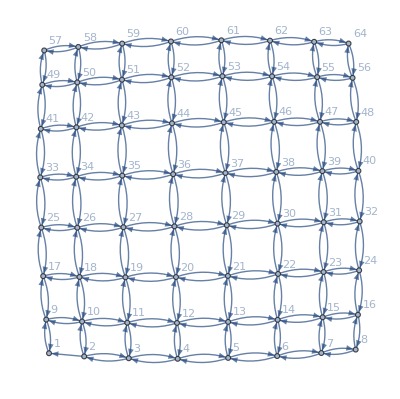

```mathematica
g2=ResourceFunction["HypergraphToGraph"][hginhomogeneities,VertexLabels->Automatic]
```

```mathematica
N@Eigenvalues@matrixLaplacian1[g2]
```

{-7.69497,-7.26197,-7.25835,-6.82256,-6.61311,-6.60685,-6.17955,-6.15957,-5.84766,-5.83974,-5.51716,-5.41394,-5.38572,-5.08207,-5.07316,-4.76515,-4.7346,-4.64778,-4.61175,-4.43288,-4.42129,-4.,-4.,-4.,-4.,-4.,-3.99422,-3.89941,-3.84718,-3.83219,-3.56279,-3.53315,-3.41225,-3.40187,-3.34633,-3.30516,-3.23348,-3.15283,-2.90969,-2.85588,-2.76057,-2.71735,-2.57921,-2.52262,-2.41137,-2.1386,-2.08617,-1.99065,-1.93822,-1.81424,-1.74745,-1.35961+0.0155732 ⅈ,-1.35961-0.0155732 ⅈ,-1.2157+0.0164867 ⅈ,-1.2157-0.0164867 ⅈ,-1.17949,-0.743217+0.0151648 ⅈ,-0.743217-0.0151648 ⅈ,-0.589998+0.00945564 ⅈ,-0.589998-0.00945564 ⅈ,-0.319204,-0.165273,-0.152794,-0.00344861}

```mathematica
circleGraph={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{6,7},{8,7},{7,7}};
```

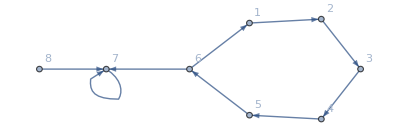

```mathematica
g3=ResourceFunction["HypergraphToGraph"][circleGraph,VertexLabels->Automatic]
```

```mathematica
N@Eigenvalues@matrixLaplacian[g3]
```

{-3.2852,-3.,-2.67137+0.784851 ⅈ,-2.67137-0.784851 ⅈ,-1.62667+0.829645 ⅈ,-1.62667-0.829645 ⅈ,-1.11873,-1.}

```mathematica
matrixLaplacian1[g_]:=Normal@AdjacencyMatrix[g]-1/2 Normal@DiagonalMatrix[VertexDegree@g];
```

```mathematica
N@Eigenvalues@matrixLaplacian1[g3]
```

{-2.10553,-1.58921+0.847798 ⅈ,-1.58921-0.847798 ⅈ,-0.573453+0.854219 ⅈ,-0.573453-0.854219 ⅈ,-0.5,-0.0691472}

```mathematica
rwLaplacian[g_]:=IdentityMatrix[Length@VertexList@g]-Dot[Inverse@Normal@DiagonalMatrix[VertexOutDegree@g],Normal@AdjacencyMatrix[g]];
```

```mathematica
Normal@AdjacencyMatrix[g3]
```

{{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,1,0},{1,0,0,0,0,0,1},{0,0,0,0,0,0,1}}

```mathematica
Normal@DiagonalMatrix[VertexOutDegree@g3]
```

{{1,0,0,0,0,0,0},{0,1,0,0,0,0,0},{0,0,1,0,0,0,0},{0,0,0,1,0,0,0},{0,0,0,0,1,0,0},{0,0,0,0,0,2,0},{0,0,0,0,0,0,1}}

```mathematica
N@Eigenvalues@rwLaplacian[g3]
```

{1.8909,1.44545+0.771541 ⅈ,1.44545-0.771541 ⅈ,1.,0.554551+0.771541 ⅈ,0.554551-0.771541 ⅈ,0.109101,0.}

```mathematica
N@Eigenvalues@rwLaplacian1[g3]
```

{1.-1. PseudoInverse[DiagonalMatrix[VertexOutDegree[g3]]].AdjacencyMatrix[g3]}